```mathematica
ρ = 0.5;
ψ = 0.5;
α = 2.39;
β = 0.3389831;
```

```mathematica
cosfun[t_,ρ_,ω_]:=1 - ρ Cos[2 π t / ω];
```

```mathematica
kernel[t_, ψ_, α_, β_] := PDF[GammaDistribution[ψ α, 1/β], t];
```

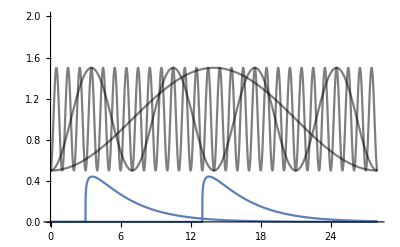

```mathematica
Show[
Plot[Table[1 - ρ Cos[2 π t / ω],{ω, {1,7,28}}],{t,0,28}, PlotRange->{0,2}, PlotStyle->{Black, Opacity[0.5]}],
Plot[2*PDF[GammaDistribution[ψ α, 1/β],t-3],{t,0,28}, PlotRange->All],
Plot[2*PDF[GammaDistribution[ψ α, 1/β],t-13],{t,0,28}, PlotRange->All]
]
```

```mathematica
periods = {1,7,28};
ρ=0.25;
ψ = 1;
scale=5;
colors={Red,Blue,Magenta};
```

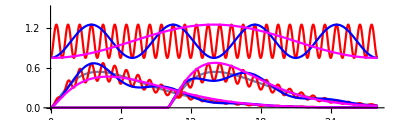

```mathematica
Show[
Table[Plot[1-ρ Cos[2 π t / periods[[i]]],{t, 0, 28}, PlotRange->{0, 1.5}, PlotStyle->colors[[i]]],{i,Length[periods]}],
Plot[scale*PDF[GammaDistribution[ψ α, 1/β],t-0],{t,0,28}, PlotRange->All],
Plot[scale*PDF[GammaDistribution[ψ α, 1/β],t-10],{t,0,28}, PlotRange->All],

Table[Plot[
scale*PDF[GammaDistribution[ψ α, 1/β],t-0]*(1 - ρ Cos[2 π t / periods[[i]]]),{t,0,28}, PlotRange->All, PlotStyle->colors[[i]]],{i,Length[periods]}],

Table[Plot[
scale*PDF[GammaDistribution[ψ α, 1/β],t-10]*(1 - ρ Cos[2 π t / periods[[i]]]),{t,0,28}, PlotRange->All, PlotStyle->colors[[i]]],{i,Length[periods]}], 
AspectRatio->.3
]
```

```mathematica
temp = {NIntegrate[cosfun[t,ρ,periods[[1]]]*kernel[t-0,ψ,α,β],{t,0,100}],
NIntegrate[cosfun[t,ρ,periods[[1]]]*kernel[t-10,ψ,α,β],{t,0,100}]}
```

{1.00021,1.00021}

```mathematica
(Max[temp] - Min[temp])/Max[temp] * 100
```

2.35463×10^-7

```mathematica
temp = {NIntegrate[cosfun[t,ρ,periods[[2]]]*kernel[t-0,ψ,α,β],{t,0,100}],
NIntegrate[cosfun[t,ρ,periods[[2]]]*kernel[t-10,ψ,α,β],{t,0,100}]}
```

{1.02015,0.984083}

```mathematica
(Max[temp] - Min[temp])/Max[temp] * 100
```

3.53533

```mathematica
temp = {NIntegrate[cosfun[t,ρ,periods[[3]]]*kernel[t-0,ψ,α,β],{t,0,100}],
NIntegrate[cosfun[t,ρ,periods[[3]]]*kernel[t-10,ψ,α,β],{t,0,100}]}
```

{0.972086,1.14211}

```mathematica
(Max[temp] - Min[temp])/Max[temp] * 100
```

14.8872

```mathematica
periods = {1,7,28};
ρ=0.25;
ψ = 0.45;
scale=2;
colors={Red,Blue,Magenta};
```

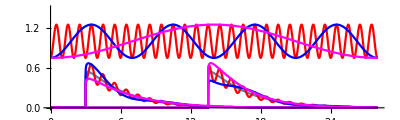

```mathematica
Show[
Table[Plot[1-ρ Cos[2 π t / periods[[i]]],{t, 0, 28}, PlotRange->{0, 1.5}, PlotStyle->colors[[i]]],{i,Length[periods]}],
Plot[scale*PDF[GammaDistribution[ψ α, 1/β],t-3],{t,0,28}, PlotRange->All],
Plot[scale*PDF[GammaDistribution[ψ α, 1/β],t-13.5],{t,0,28}, PlotRange->All],

Table[Plot[
scale*PDF[GammaDistribution[ψ α, 1/β],t-3]*(1 - ρ Cos[2 π t / periods[[i]]]),{t,0,28}, PlotRange->All, PlotStyle->colors[[i]]],{i,Length[periods]}],

Table[Plot[
scale*PDF[GammaDistribution[ψ α, 1/β],t-13.5]*(1 - ρ Cos[2 π t / periods[[i]]]),{t,0,28}, PlotRange->All, PlotStyle->colors[[i]]],{i,Length[periods]}], 
AspectRatio->.3
]
```

```mathematica
temp = {NIntegrate[cosfun[t,ρ,periods[[1]]]*kernel[t-0,ψ,α,β],{t,0,100}],
NIntegrate[cosfun[t,ρ,periods[[1]]]*kernel[t-10,ψ,α,β],{t,0,100}]}
```

{1.00065,1.00065}

```mathematica
(Max[temp] - Min[temp])/Max[temp] * 100
```

7.2783×10^-12

```mathematica
temp = {NIntegrate[cosfun[t,ρ,periods[[2]]]*kernel[t-0,ψ,α,β],{t,0,100}],
NIntegrate[cosfun[t,ρ,periods[[2]]]*kernel[t-10,ψ,α,β],{t,0,100}]}
```

{0.978239,1.05375}

```mathematica
(Max[temp] - Min[temp])/Max[temp] * 100
```

7.1661

```mathematica
temp = {NIntegrate[cosfun[t,ρ,periods[[3]]]*kernel[t-0,ψ,α,β],{t,0,100}],
NIntegrate[cosfun[t,ρ,periods[[3]]]*kernel[t-10,ψ,α,β],{t,0,100}]}
```

{0.833718,1.19824}

```mathematica
(Max[temp] - Min[temp])/Max[temp] * 100
```

30.4217

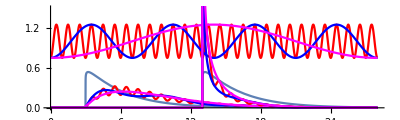

```mathematica
ψ1 = 0.8;
ψ2 = 0.2;
Show[
Table[Plot[1-ρ Cos[2 π t / periods[[i]]],{t, 0, 28}, PlotRange->{0, 1.5}, PlotStyle->colors[[i]]],{i,Length[periods]}],
Plot[scale*PDF[GammaDistribution[ψ α, 1/β],t-3],{t,0,28}, PlotRange->All],
Plot[scale*PDF[GammaDistribution[ψ α, 1/β],t-13],{t,0,28}, PlotRange->All],

Table[Plot[
scale*PDF[GammaDistribution[ψ1 α, 1/β],t-3]*(1 - ρ Cos[2 π t / periods[[i]]]),{t,0,28}, PlotRange->All, PlotStyle->colors[[i]]],{i,Length[periods]}],

Table[Plot[
scale*PDF[GammaDistribution[ψ2 α, 1/β],t-13]*(1 - ρ Cos[2 π t / periods[[i]]]),{t,0,28}, PlotRange->All, PlotStyle->colors[[i]]],{i,Length[periods]}], 
AspectRatio->.3
]
```

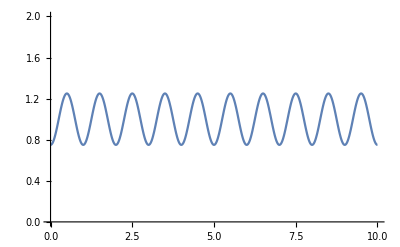

```mathematica
Plot[cosfun[t, ρ, 1],{t, 0, 10}, PlotRange->{0,2}]
```

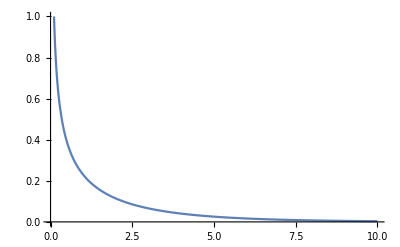

```mathematica
Plot[kernel[t, .2, α, β], {t, 0, 10}, PlotRange->{0,1}]
```

```mathematica
temp = Table[NIntegrate[kernel[t, .2, α, β]*cosfun[t, ρ, 1],{t,0,tmax}],{tmax, 0, 10, 0.01}];
```

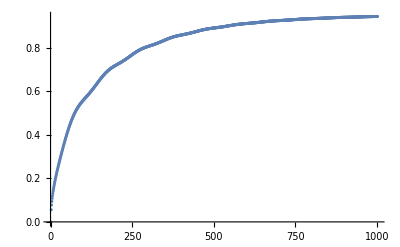

```mathematica
ListPlot[temp]
```

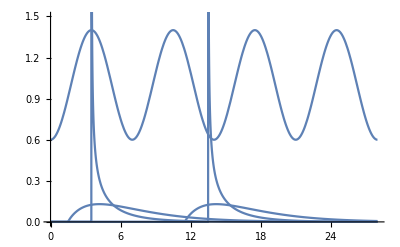

```mathematica
Show[
Plot[cosfun[t, .4, 7],{t,0,28}, PlotRange->{0,1.5}],
Plot[kernel[t-3.5, 0.2, α,β],{t,0,28}, PlotRange->All],
Plot[kernel[t-1.5, 0.8, α,β],{t,0,28}, PlotRange->{0, All}],
Plot[kernel[t-13.5, 0.2, α,β],{t,0,28}, PlotRange->All],
Plot[kernel[t-11.5, 0.8, α,β],{t,0,28}, PlotRange->{0, All}]
]
```

```mathematica
tmaxvals = Range[0, 25, 0.1];
```

```mathematica
temp1 = Table[NIntegrate[
cosfun[t, 1, 7]*kernel[t-3.5, 0.3, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp2 = Table[NIntegrate[
cosfun[t, 1, 7]*kernel[t-1.5, 0.7, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp3 = Table[NIntegrate[
cosfun[t, 1, 7]*kernel[t-13.5, 0.3, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp4 = Table[NIntegrate[
cosfun[t, 1, 7]*kernel[t-11.5, 0.7, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
```

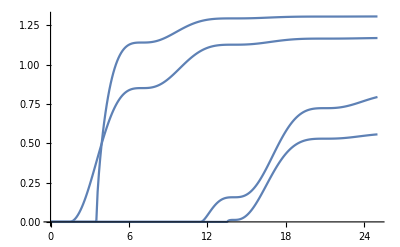

```mathematica
Show[
ListLinePlot[{tmaxvals,temp1}ᵀ],
ListLinePlot[{tmaxvals,temp2}ᵀ],
ListLinePlot[{tmaxvals,temp3}ᵀ],
ListLinePlot[{tmaxvals,temp4}ᵀ]
]
```

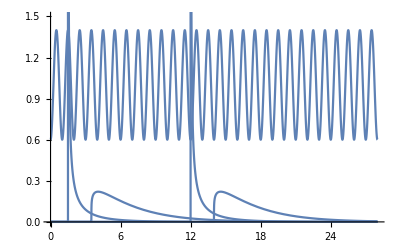

```mathematica
Show[
Plot[cosfun[t, .4, 1],{t,0,28}, PlotRange->{0,1.5}],
Plot[kernel[t-3.5, 0.5, α,β],{t,0,28}, PlotRange->All],
Plot[kernel[t-1.5, 0.1, α,β],{t,0,28}, PlotRange->{0, All}],
Plot[kernel[t-14, 0.5, α,β],{t,0,28}, PlotRange->All],
Plot[kernel[t-12, 0.1, α,β],{t,0,28}, PlotRange->{0, All}]
]
```

```mathematica
tmaxvals = Range[0, 40, 0.1];
```

```mathematica
temp1 = Table[NIntegrate[
cosfun[t, 1, .5]*kernel[t-3.5, 0.2, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp2 = Table[NIntegrate[
cosfun[t, 1,.5]*kernel[t-1.5, 0.8, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp3 = Table[NIntegrate[
cosfun[t, 1, .5]*kernel[t-14, 0.2, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp4 = Table[NIntegrate[
cosfun[t, 1,.5]*kernel[t-12, 0.8, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
```

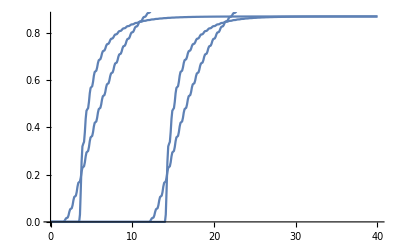

```mathematica
Show[
ListLinePlot[{tmaxvals,temp1}ᵀ],
ListLinePlot[{tmaxvals,temp2}ᵀ],
ListLinePlot[{tmaxvals,temp3}ᵀ],
ListLinePlot[{tmaxvals,temp4}ᵀ]
]
```

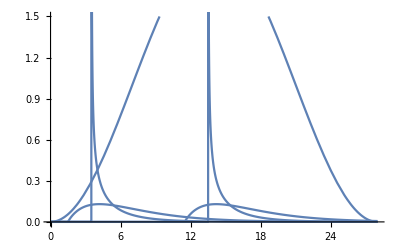

```mathematica
Show[
Plot[cosfun[t, 1, 28],{t,0,28}, PlotRange->{0,1.5}],
Plot[kernel[t-3.5, 0.2, α,β],{t,0,28}, PlotRange->All],
Plot[kernel[t-1.5, 0.8, α,β],{t,0,28}, PlotRange->{0, All}],
Plot[kernel[t-13.5, 0.2, α,β],{t,0,28}, PlotRange->All],
Plot[kernel[t-11.5, 0.8, α,β],{t,0,28}, PlotRange->{0, All}]
]
```

```mathematica
tmaxvals = Range[0, 40, 0.1];
```

```mathematica
temp1 = Table[NIntegrate[
cosfun[t, 1, 28]*kernel[t-3.5, 0.2, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp2 = Table[NIntegrate[
cosfun[t, 1, 28]*kernel[t-1.5, 0.8, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp3 = Table[NIntegrate[
cosfun[t, 1, 28]*kernel[t-13.5, 0.2, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
temp4 = Table[NIntegrate[
cosfun[t, 1, 28]*kernel[t-11.5, 0.8, α,β]
,{t,0,tmax}],{tmax,tmaxvals}];
```

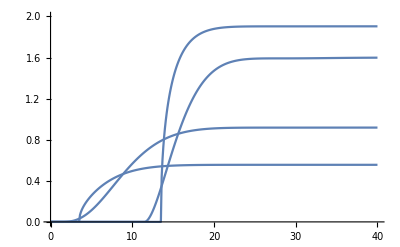

```mathematica
Show[
ListLinePlot[{tmaxvals,temp1}ᵀ, PlotRange->{0,2}],
ListLinePlot[{tmaxvals,temp2}ᵀ],
ListLinePlot[{tmaxvals,temp3}ᵀ],
ListLinePlot[{tmaxvals,temp4}ᵀ]
]
```